```mathematica
观察角度与角速度之间的相位关系
```

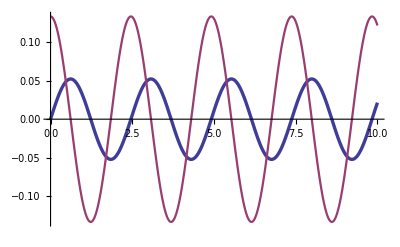

```mathematica
g=9.8;L=1.5;Ω=√(g/L);
v0=0.2;ω0=v0/L;
s=NDSolve[{θ''[t]==-Ω^2*Sin[θ[t]],
θ[0]==0,θ'[0]==ω0},θ,{t,0,10}];
θ=θ/.s[[1]];
Plot[{θ[t],θ'[t]},{t,0,10},
PlotStyle->{Thickness[0.006],Thickness[0.004]},
AxesStyle->Thickness[0.003]]
Clear[g,L,Ω,v0,ω0,s,θ]
```